```mathematica
Clear[m,B, R]
$Assumptions={Element[{x,y, Ω, ν, t,x,y, R},Reals], Element[{ζ,α,z},Complexes], Element[{n, m}, Integers],x>0, t>0, α>0, m>0, n>0};
R =0 ;
r = α +(1-α)x;
w0f = 1/4(2Log[r/α]-(r^2-α^2));
w0 = Normal[Series[Integrate[w0f, {x,0,1}], {α, 1, 2}]]
m=1;
w = A Sin[m π x]
u1 = I k Integrate[w, x];
u = u1 - (u1/.x->0)
p=FullSimplify[I/k(R(Λ u + I k w0 w+w D[w0, x])-D[D[w, x],x]+k^2 w)]
eqNSx=R I k w0 u+R Λ u+D[p,x]-D[D[u,x],x]+k^2 u;
eq1=Simplify@Integrate[eqNSx Sin[π x], {x, 0,1}]
eq2=Simplify@Integrate[eqNSx Cos[π x], {x, 0,1}]
kinematic = FullSimplify@((Λ S + w0 I k S-u)/. x->1)
normalstress = FullSimplify@((Bo p - 2Ca D[u,x] +D S -k^2 S)/. x->1)
```

1/3 (-1+α)^2

A Sin[π x]

(ⅈ A k)/π-(ⅈ A k Cos[π x])/π

(ⅈ A (k^2+π^2) Sin[π x])/k

(2 ⅈ A k^3)/π^2

(ⅈ A (-k^4+π^4))/(2 k π)

-(2 ⅈ A k)/π+1/3 ⅈ k S (-1+α)^2+S Λ

(D-k^2) S

```mathematica
matrix = FullSimplify@{{SeriesCoefficient[eq1, {A, 0, 1}], SeriesCoefficient[eq1, {B, 0, 1}],SeriesCoefficient[eq1, {C, 0, 1}], SeriesCoefficient[eq1, {S, 0, 1}]}, 
{SeriesCoefficient[eq2, {A, 0, 1}], SeriesCoefficient[eq2, {B, 0, 1}], SeriesCoefficient[eq2, {C, 0, 1}], SeriesCoefficient[eq2, {S, 0, 1}]}, 
{SeriesCoefficient[kinematic, {A, 0, 1}], SeriesCoefficient[kinematic, {B, 0, 1}], SeriesCoefficient[kinematic, {C, 0, 1}], SeriesCoefficient[kinematic, {S, 0, 1}]}, 
{SeriesCoefficient[normalstress, {A, 0, 1}], SeriesCoefficient[normalstress, {B, 0, 1}], SeriesCoefficient[normalstress, {C, 0, 1}], SeriesCoefficient[normalstress, {S, 0, 1}]}};
MatrixForm[matrix]
```

((2 ⅈ k^3)/π^2 | -(ⅈ (k^4+π^4))/(2 k π) | (ⅈ k^3 (-4+π^2))/(2 π^3) | 0
(ⅈ (-k^4+π^4))/(2 k π) | (2 ⅈ k^3)/π^2 | -(ⅈ k^3)/π^2 | 0
-(2 ⅈ k)/π | ⅈ k | -(ⅈ k)/2 | 1/3 ⅈ k (-1+α)^2+Λ
0 | -(ⅈ (2 (Bo-2 Ca) k^2+Bo π^2))/k | ⅈ (Bo-2 Ca) k | D-k^2)

```mathematica
matrixdet = Det[matrix]
```

(D-k^2) (2 ⅈ k^3+(8 ⅈ k^7)/π^6-(2 ⅈ k^7)/π^4+(ⅈ k^7)/(8 π^2)-1/4 ⅈ k^3 π^2+(ⅈ π^6)/(8 k))-((ⅈ (2 (Bo-2 Ca) k^2+Bo π^2) (-k^2+(3 k^6)/π^4-k^6/(4 π^2)+(k^2 π^2)/4))/k+ⅈ (Bo-2 Ca) k (-(4 k^6)/π^4+k^6/(4 π^2)-π^6/(4 k^2))) (1/3 ⅈ k (-1+α)^2+Λ)

```mathematica
c0 = matrixdet /. Λ->0
c1 = SeriesCoefficient[matrixdet, {Λ, 0, 1}]
c2 = SeriesCoefficient[matrixdet, {Λ, 0, 2}]
```

(D-k^2) (2 ⅈ k^3+(8 ⅈ k^7)/π^6-(2 ⅈ k^7)/π^4+(ⅈ k^7)/(8 π^2)-1/4 ⅈ k^3 π^2+(ⅈ π^6)/(8 k))-1/3 ⅈ k ((ⅈ (2 (Bo-2 Ca) k^2+Bo π^2) (-k^2+(3 k^6)/π^4-k^6/(4 π^2)+(k^2 π^2)/4))/k+ⅈ (Bo-2 Ca) k (-(4 k^6)/π^4+k^6/(4 π^2)-π^6/(4 k^2))) (-1+α)^2

-(ⅈ (2 (Bo-2 Ca) k^2+Bo π^2) (-k^2+(3 k^6)/π^4-k^6/(4 π^2)+(k^2 π^2)/4))/k-ⅈ (Bo-2 Ca) k (-(4 k^6)/π^4+k^6/(4 π^2)-π^6/(4 k^2))

0

```mathematica
lambdaguess = FullSimplify[-c0/c1]
```

(ⅈ (3 ⅈ (D-k^2) (π^6-k^4 (-8+π^2))^2+2 k ((Bo-2 Ca) (-π^10+k^8 (-16+π^2))+(2 (Bo-2 Ca) k^2+Bo π^2) (-k^6 (-12+π^2)+k^2 π^4 (-4+π^2))) (π-π α)^2))/(6 π^2 (-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2))))

```mathematica
ComplexExpand[lambdaguess];
```

```mathematica
lambdaguessreal = FullSimplify[(8 D k^8)/(-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2)))-(8 k^10)/(-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2)))-(32 D k^8)/(π^2 (-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2))))+(32 k^10)/(π^2 (-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2))))-(D k^8 π^2)/(2 (-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2))))+(k^10 π^2)/(2 (-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2))))-(8 D k^4 π^4)/(-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2)))+(8 k^6 π^4)/(-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2)))+(D k^4 π^6)/(-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2)))-(k^6 π^6)/(-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2)))-(D π^10)/(2 (-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2))))+(k^2 π^10)/(2 (-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2))))]
```

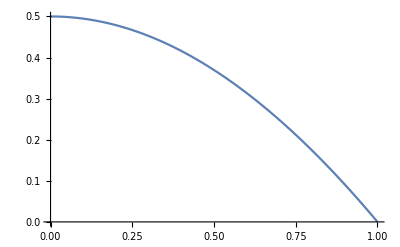

```mathematica
Plot[0.1(-(((D-k^2) (π^6-k^4 (-8+π^2))^2)/(2 π^2 (-2 Ca (π^10+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2))+Bo (π^10+k^6 π^2 (-12+π^2)+k^8 (-8+π^2)-2 k^4 π^4 (-4+π^2)-k^2 π^6 (-4+π^2))))))/. {Ca->0.1, Bo->0.1, D->1}, {k, 0,1}]
```